```mathematica
1+1
```

2

```mathematica
collatzNextState[n_Integer]:=Piecewise[{{1, n==1}, {n/2, EvenQ[n]}, {3n+1, OddQ[n]}}]
```

```mathematica
collatzNextState[3]
```

10

```mathematica
Table[collatzNextState[i], {i, 1, 10}]
```

{1,1,10,2,16,3,22,4,28,5}

```mathematica
Table[i->collatzNextState[i], {i, 1, 10}]
```

{1→1,2→1,3→10,4→2,5→16,6→3,7→22,8→4,9→28,10→5}

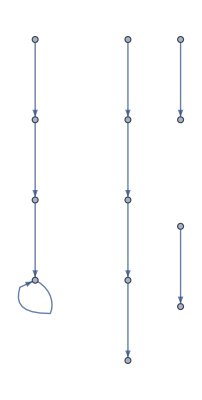

```mathematica
Graph[
Table[i->collatzNextState[i], {i, 1, 10}]]
```

```mathematica
Table[{Labeled[i,i],
Labeled[collatzNextState[i],collatzNextState[i]]}, {i, 1, 10}]
```

{{11,11},{22,11},{33,1010},{44,22},{55,1616},{66,33},{77,2222},{88,44},{99,2828},{1010,55}}

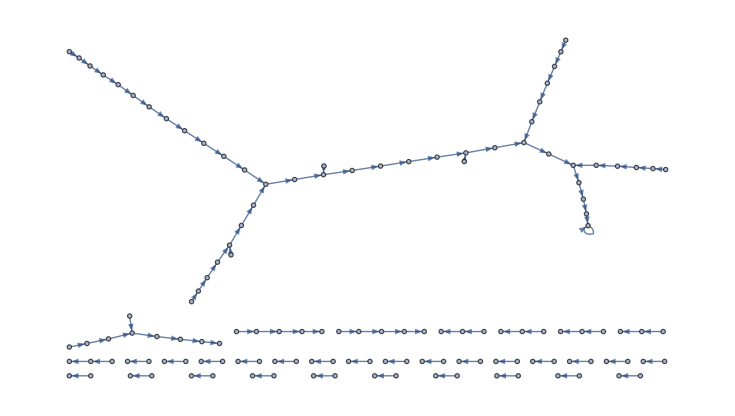

```mathematica
Graph[
Table[i->collatzNextState[i], {i, 1, 100}]]
```

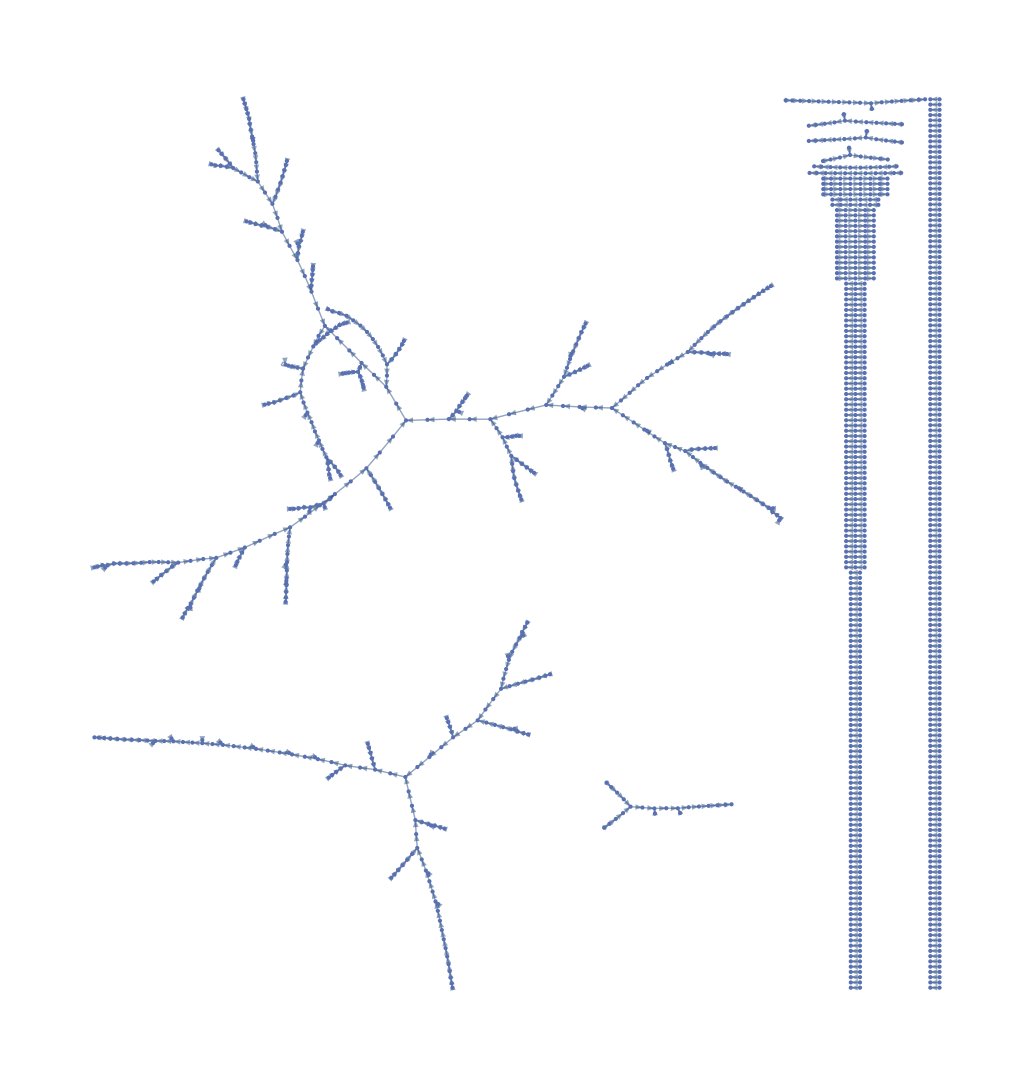

```mathematica
Graph[
Table[i->collatzNextState[i], {i, 1, 1000}]]
```

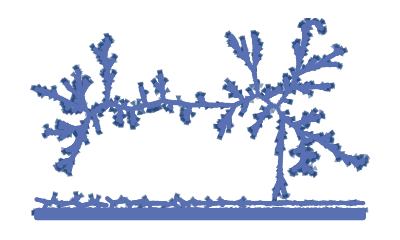

```mathematica
Graph[
Table[i->collatzNextState[i], {i, 1, 10000}]]
```

```mathematica
FindIndependentEdgeSet[%138]
```

{2->1,6->3,20->10,8->4,5->16,14->7,6120,9991->29974,9993->29980,9995->29986,9997->29992,9999->29998}
 |  |  |  |



```mathematica
CompleteGraph[2]
```

```mathematica
FindIndependentVertexSet[
GridGraph[{4,4}]]
```

{{1,3,6,8,9,11,14,16}}

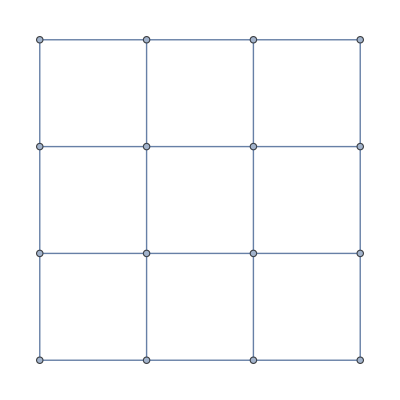

```mathematica
GridGraph[{4,4}]
```

```mathematica
Manipulate[
Graph[
Table[i->collatzNextState[i], {i, 1, a}],
GraphLayout->"RadialEmbedding"],
{a,1,10000,1}]
```

```mathematica
NestWhile[collatzNextState, i, 1==#&]
```

i

```mathematica
NestWhile[collatzNextState, 1, 1==#&]
```

$Aborted

```mathematica
NestWhile[collatzNextState, 2, 1==#&,1]
```

2

```mathematica
NestWhileList[collatzNextState, 10, 1==#&,1]
```

{10}

```mathematica
collatzGraph[list_,n_]:=Piecewise[{{Join[list,{1->1}], n==1}, {collatzNextState[Join[list,{n->n/2}],n/2], EvenQ[n]}, {collatzNextState[Join[list,{n->3n+1}],3n+1], OddQ[n]}}]
```

```mathematica
Clear[collatzGraph]
```

```mathematica
collatzGraph[list_,n_Integer]:=Piecewise[{{Join[list,{1->1}], n==1}, {collatzNextState[Join[list,{n->n/2}],n/2], EvenQ[n]}, {collatzNextState[Join[list,{n->3n+1}],3n+1], OddQ[n]}}]
```

```mathematica
collatzGraph[{},1]
```

{1→1}

```mathematica
collatzGraph[{},2]
```

collatzNextState[{2→1},1]

```mathematica
collatzGraph[{},3]
```

collatzNextState[{3→10},10]

```mathematica
Clear[collatzGraph]
```

```mathematica
collatzGraph[list_,n_Integer]:=Piecewise[{{Join[list,{1->1}], n==1}, {collatzGraph[Join[list,{n->n/2}],n/2], EvenQ[n]}, {collatzGraph[Join[list,{n->3n+1}],3n+1], OddQ[n]}}]
```

```mathematica
collatzGraph[{},3]
```

{3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1}

```mathematica
collatzGraph[{},10]
```

{10→5,5→16,16→8,8→4,4→2,2→1,1→1}

```mathematica
collatzGraph[{},101]
```

{101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1}

```mathematica
{1,2,1}
```

{1,2,1}

```mathematica
DeleteDuplicates[{1,2,1}]
```

{1,2}

```mathematica
DeleteDuplicates[{101->304,304->152,152->76,76->38,38->19,19->58,58->29,29->88,88->44,44->22,22->11,11->34,34->17,17->52,52->26,26->13,13->40,40->20,20->10,10->5,5->16,16->8,8->4,4->2,2->1,1->1,1->1}]
```

{101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1}

```mathematica
Flatten[
Table[collatzGraph[{},i],{i,1,100}]
,1]
```

{1→1,2→1,1→1,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,4→2,2→1,1→1,5→16,16→8,8→4,4→2,2→1,1→1,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,8→4,4→2,2→1,1→1,9→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,10→5,5→16,16→8,8→4,4→2,2→1,1→1,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,12→6,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,15→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,16→8,8→4,4→2,2→1,1→1,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,18→9,9→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,21→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,24→12,12→6,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,27→82,82→41,41→124,124→62,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,30→15,15→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,32→16,16→8,8→4,4→2,2→1,1→1,33→100,100→50,50→25,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,36→18,18→9,9→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,39→118,118→59,59→178,178→89,89→268,268→134,134→67,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,41→124,124→62,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,42→21,21→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,43→130,130→65,65→196,196→98,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,45→136,136→68,68→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,48→24,24→12,12→6,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,50→25,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,51→154,154→77,77→232,232→116,116→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,54→27,27→82,82→41,41→124,124→62,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,55→166,166→83,83→250,250→125,125→376,376→188,188→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,57→172,172→86,86→43,43→130,130→65,65→196,196→98,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,59→178,178→89,89→268,268→134,134→67,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,60→30,30→15,15→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,63→190,190→95,95→286,286→143,143→430,430→215,215→646,646→323,323→970,970→485,485→1456,1456→728,728→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,64→32,32→16,16→8,8→4,4→2,2→1,1→1,65→196,196→98,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,66→33,33→100,100→50,50→25,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,68→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,69→208,208→104,104→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,72→36,36→18,18→9,9→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,73→220,220→110,110→55,55→166,166→83,83→250,250→125,125→376,376→188,188→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,75→226,226→113,113→340,340→170,170→85,85→256,256→128,128→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,77→232,232→116,116→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,78→39,39→118,118→59,59→178,178→89,89→268,268→134,134→67,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,79→238,238→119,119→358,358→179,179→538,538→269,269→808,808→404,404→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,81→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,82→41,41→124,124→62,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,83→250,250→125,125→376,376→188,188→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,84→42,42→21,21→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,85→256,256→128,128→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,86→43,43→130,130→65,65→196,196→98,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,87→262,262→131,131→394,394→197,197→592,592→296,296→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,89→268,268→134,134→67,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,90→45,45→136,136→68,68→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,93→280,280→140,140→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,95→286,286→143,143→430,430→215,215→646,646→323,323→970,970→485,485→1456,1456→728,728→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,96→48,48→24,24→12,12→6,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,97→292,292→146,146→73,73→220,220→110,110→55,55→166,166→83,83→250,250→125,125→376,376→188,188→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,99→298,298→149,149→448,448→224,224→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,100→50,50→25,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1}

```mathematica
Flatten[
DeleteDuplicates[
Table[collatzGraph[{},i],{i,1,100}]]
,1]
```

{1→1,2→1,1→1,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,4→2,2→1,1→1,5→16,16→8,8→4,4→2,2→1,1→1,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,8→4,4→2,2→1,1→1,9→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,10→5,5→16,16→8,8→4,4→2,2→1,1→1,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,12→6,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,15→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,16→8,8→4,4→2,2→1,1→1,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,18→9,9→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,21→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,24→12,12→6,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,27→82,82→41,41→124,124→62,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,30→15,15→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,32→16,16→8,8→4,4→2,2→1,1→1,33→100,100→50,50→25,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,36→18,18→9,9→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,39→118,118→59,59→178,178→89,89→268,268→134,134→67,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,41→124,124→62,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,42→21,21→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,43→130,130→65,65→196,196→98,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,45→136,136→68,68→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,48→24,24→12,12→6,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,50→25,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,51→154,154→77,77→232,232→116,116→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,54→27,27→82,82→41,41→124,124→62,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,55→166,166→83,83→250,250→125,125→376,376→188,188→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,57→172,172→86,86→43,43→130,130→65,65→196,196→98,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,59→178,178→89,89→268,268→134,134→67,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,60→30,30→15,15→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,63→190,190→95,95→286,286→143,143→430,430→215,215→646,646→323,323→970,970→485,485→1456,1456→728,728→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,64→32,32→16,16→8,8→4,4→2,2→1,1→1,65→196,196→98,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,66→33,33→100,100→50,50→25,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,68→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,69→208,208→104,104→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,72→36,36→18,18→9,9→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,73→220,220→110,110→55,55→166,166→83,83→250,250→125,125→376,376→188,188→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,75→226,226→113,113→340,340→170,170→85,85→256,256→128,128→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,77→232,232→116,116→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,78→39,39→118,118→59,59→178,178→89,89→268,268→134,134→67,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,79→238,238→119,119→358,358→179,179→538,538→269,269→808,808→404,404→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,81→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,82→41,41→124,124→62,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,83→250,250→125,125→376,376→188,188→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,84→42,42→21,21→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,85→256,256→128,128→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,86→43,43→130,130→65,65→196,196→98,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,87→262,262→131,131→394,394→197,197→592,592→296,296→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,89→268,268→134,134→67,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,90→45,45→136,136→68,68→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,93→280,280→140,140→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,95→286,286→143,143→430,430→215,215→646,646→323,323→970,970→485,485→1456,1456→728,728→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,96→48,48→24,24→12,12→6,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,97→292,292→146,146→73,73→220,220→110,110→55,55→166,166→83,83→250,250→125,125→376,376→188,188→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,99→298,298→149,149→448,448→224,224→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,100→50,50→25,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1}

```mathematica
Graph[
Flatten[
Table[collatzGraph[{},i],{i,1,100}]
,1]]
```

-Graphics-

```mathematica
Graph[
Flatten[
Table[collatzGraph[{},i],{i,1,100}]
,1], GraphLayout->"RadialEmbedding"]
```

-Graphics-

```mathematica
Graph[
Flatten[
Table[collatzGraph[{},i],{i,1,100}]
,1], GraphLayout->"RadialEmbedding"]
```

-Graphics-

```mathematica
ConnectedGraphQ[%172]
```

False

```mathematica
AcyclicGraphQ[%172]
```

True

```mathematica
Flatten[
Table[collatzGraph[{},i],{i,1,100}]
,1]
```

{1→1,2→1,1→1,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,4→2,2→1,1→1,5→16,16→8,8→4,4→2,2→1,1→1,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,8→4,4→2,2→1,1→1,9→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,10→5,5→16,16→8,8→4,4→2,2→1,1→1,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,12→6,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,15→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,16→8,8→4,4→2,2→1,1→1,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,18→9,9→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,21→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,24→12,12→6,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,27→82,82→41,41→124,124→62,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,30→15,15→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,32→16,16→8,8→4,4→2,2→1,1→1,33→100,100→50,50→25,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,36→18,18→9,9→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,39→118,118→59,59→178,178→89,89→268,268→134,134→67,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,41→124,124→62,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,42→21,21→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,43→130,130→65,65→196,196→98,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,45→136,136→68,68→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,48→24,24→12,12→6,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,50→25,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,51→154,154→77,77→232,232→116,116→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,54→27,27→82,82→41,41→124,124→62,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,55→166,166→83,83→250,250→125,125→376,376→188,188→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,57→172,172→86,86→43,43→130,130→65,65→196,196→98,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,59→178,178→89,89→268,268→134,134→67,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,60→30,30→15,15→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,63→190,190→95,95→286,286→143,143→430,430→215,215→646,646→323,323→970,970→485,485→1456,1456→728,728→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,64→32,32→16,16→8,8→4,4→2,2→1,1→1,65→196,196→98,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,66→33,33→100,100→50,50→25,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,68→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,69→208,208→104,104→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,72→36,36→18,18→9,9→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,73→220,220→110,110→55,55→166,166→83,83→250,250→125,125→376,376→188,188→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,75→226,226→113,113→340,340→170,170→85,85→256,256→128,128→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,77→232,232→116,116→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,78→39,39→118,118→59,59→178,178→89,89→268,268→134,134→67,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,79→238,238→119,119→358,358→179,179→538,538→269,269→808,808→404,404→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,81→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,82→41,41→124,124→62,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,83→250,250→125,125→376,376→188,188→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,84→42,42→21,21→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,85→256,256→128,128→64,64→32,32→16,16→8,8→4,4→2,2→1,1→1,86→43,43→130,130→65,65→196,196→98,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,87→262,262→131,131→394,394→197,197→592,592→296,296→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,89→268,268→134,134→67,67→202,202→101,101→304,304→152,152→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,90→45,45→136,136→68,68→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,93→280,280→140,140→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,95→286,286→143,143→430,430→215,215→646,646→323,323→970,970→485,485→1456,1456→728,728→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,96→48,48→24,24→12,12→6,6→3,3→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,97→292,292→146,146→73,73→220,220→110,110→55,55→166,166→83,83→250,250→125,125→376,376→188,188→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,98→49,49→148,148→74,74→37,37→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,99→298,298→149,149→448,448→224,224→112,112→56,56→28,28→14,14→7,7→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1,100→50,50→25,25→76,76→38,38→19,19→58,58→29,29→88,88→44,44→22,22→11,11→34,34→17,17→52,52→26,26→13,13→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1}

```mathematica
Length@%
```

3242

```mathematica
Length@DeleteDuplicates@Flatten[
Table[collatzGraph[{},i],{i,1,100}]
,1]
```

251

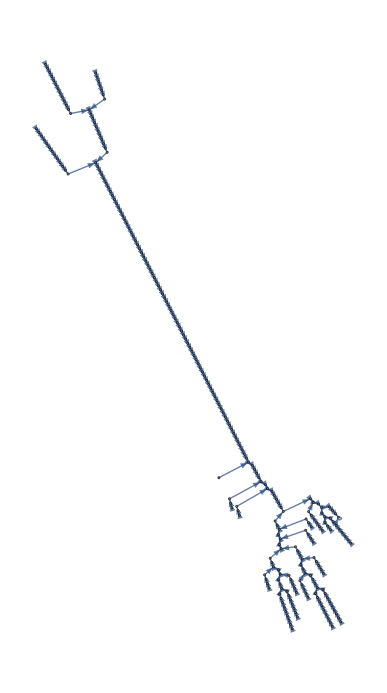

```mathematica
Graph[
DeleteDuplicates@Flatten[
Table[collatzGraph[{},i],{i,1,100}]
,1],
GraphLayout->"RadialEmbedding"]
```

```mathematica
Manipulate[
	Graph[
DeleteDuplicates@Flatten[
Table[collatzGraph[{},i],{i,1,a}]
,1],
GraphLayout->"RadialEmbedding"],
{a, 0, 100, 1}]
```

```mathematica
collatzGraph[{},27]
```

{27→82,82→41,41→124,124→62,62→31,31→94,94→47,47→142,142→71,71→214,214→107,107→322,322→161,161→484,484→242,242→121,121→364,364→182,182→91,91→274,274→137,137→412,412→206,206→103,103→310,310→155,155→466,466→233,233→700,700→350,350→175,175→526,526→263,263→790,790→395,395→1186,1186→593,593→1780,1780→890,890→445,445→1336,1336→668,668→334,334→167,167→502,502→251,251→754,754→377,377→1132,1132→566,566→283,283→850,850→425,425→1276,1276→638,638→319,319→958,958→479,479→1438,1438→719,719→2158,2158→1079,1079→3238,3238→1619,1619→4858,4858→2429,2429→7288,7288→3644,3644→1822,1822→911,911→2734,2734→1367,1367→4102,4102→2051,2051→6154,6154→3077,3077→9232,9232→4616,4616→2308,2308→1154,1154→577,577→1732,1732→866,866→433,433→1300,1300→650,650→325,325→976,976→488,488→244,244→122,122→61,61→184,184→92,92→46,46→23,23→70,70→35,35→106,106→53,53→160,160→80,80→40,40→20,20→10,10→5,5→16,16→8,8→4,4→2,2→1,1→1}

```mathematica
88000/3
```

88000/3

```mathematica
N[88000/3]
```

29333.3

```mathematica
30000
```

```mathematica
30000 * .24 * 2
```

14400.

```mathematica
30000 * .24
```

7200.

```mathematica
12 200
```

2400

```mathematica
1123-166.30
```

956.7

```mathematica
25000*4
```

100000

```mathematica
25000*4
```

100000

```mathematica
25000/500
```

50

```mathematica
50 20
```

1000

```mathematica
{115, 115, 115, 115, 115, 400, 400, 400}
```

{115,115,115,115,115,400,400,400}

```mathematica
Total[{115,115,115,115,115,400,400,400}]
```

1775

```mathematica
550 2 .20
```

220.

```mathematica
collatzNextState[4]
```

2

```mathematica
DiscretePlot[collatzNextState, {i, 1, 100}]
```

-Graphics-

```mathematica
DiscretePlot[collatzNextState, {i, 1, 10}]
```

-Graphics-

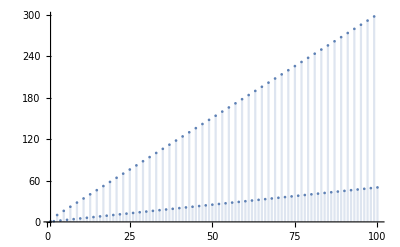

```mathematica
DiscretePlot[collatzNextState[i], {i, 1, 100}]
```

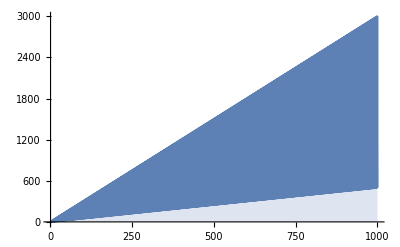

```mathematica
DiscretePlot[collatzNextState[i], {i, 1, 1000}]
```

```mathematica
Show[{
DiscretePlot[collatzNextState[i], {i, 1, 100}],
Plot[x,{x,0,100}]}]
```

Plot::itraw: Raw object  x cannot be used as an iterator.

Show::gcomb: Could not combine the graphics objects in Show[{,Plot[x, {x,0,100}]}].

Show[{-Graphics-,Plot[x, {x,0,100}]}]

```mathematica
Plot[x,{x,0,100}]
```

Plot::itraw: Raw object  x cannot be used as an iterator.

Plot[x, {x,0,100}]

```mathematica
Plot[x,{x,0,100}]
```

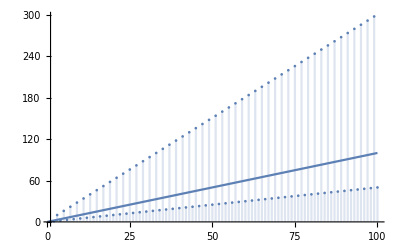

```mathematica
Show[{
DiscretePlot[collatzNextState[i], {i, 1, 100}],
Plot[x,{x,0,100}]}]
```

```mathematica
Map[{First[#],Last[#]}&,collatzGraph[{},27]]
```

{{27,82},{82,41},{41,124},{124,62},{62,31},{31,94},{94,47},{47,142},{142,71},{71,214},{214,107},{107,322},{322,161},{161,484},{484,242},{242,121},{121,364},{364,182},{182,91},{91,274},{274,137},{137,412},{412,206},{206,103},{103,310},{310,155},{155,466},{466,233},{233,700},{700,350},{350,175},{175,526},{526,263},{263,790},{790,395},{395,1186},{1186,593},{593,1780},{1780,890},{890,445},{445,1336},{1336,668},{668,334},{334,167},{167,502},{502,251},{251,754},{754,377},{377,1132},{1132,566},{566,283},{283,850},{850,425},{425,1276},{1276,638},{638,319},{319,958},{958,479},{479,1438},{1438,719},{719,2158},{2158,1079},{1079,3238},{3238,1619},{1619,4858},{4858,2429},{2429,7288},{7288,3644},{3644,1822},{1822,911},{911,2734},{2734,1367},{1367,4102},{4102,2051},{2051,6154},{6154,3077},{3077,9232},{9232,4616},{4616,2308},{2308,1154},{1154,577},{577,1732},{1732,866},{866,433},{433,1300},{1300,650},{650,325},{325,976},{976,488},{488,244},{244,122},{122,61},{61,184},{184,92},{92,46},{46,23},{23,70},{70,35},{35,106},{106,53},{53,160},{160,80},{80,40},{40,20},{20,10},{10,5},{5,16},{16,8},{8,4},{4,2},{2,1},{1,1}}

```mathematica
Flatten[
Map[
{First[#],Last[#]}&,
collatzGraph[{},27]],
1]
```

{27,82,82,41,41,124,124,62,62,31,31,94,94,47,47,142,142,71,71,214,214,107,107,322,322,161,161,484,484,242,242,121,121,364,364,182,182,91,91,274,274,137,137,412,412,206,206,103,103,310,310,155,155,466,466,233,233,700,700,350,350,175,175,526,526,263,263,790,790,395,395,1186,1186,593,593,1780,1780,890,890,445,445,1336,1336,668,668,334,334,167,167,502,502,251,251,754,754,377,377,1132,1132,566,566,283,283,850,850,425,425,1276,1276,638,638,319,319,958,958,479,479,1438,1438,719,719,2158,2158,1079,1079,3238,3238,1619,1619,4858,4858,2429,2429,7288,7288,3644,3644,1822,1822,911,911,2734,2734,1367,1367,4102,4102,2051,2051,6154,6154,3077,3077,9232,9232,4616,4616,2308,2308,1154,1154,577,577,1732,1732,866,866,433,433,1300,1300,650,650,325,325,976,976,488,488,244,244,122,122,61,61,184,184,92,92,46,46,23,23,70,70,35,35,106,106,53,53,160,160,80,80,40,40,20,20,10,10,5,5,16,16,8,8,4,4,2,2,1,1,1}

```mathematica
DeleteDuplicates[
Flatten[
Map[
{First[#],Last[#]}&,
collatzGraph[{},27]],
1]]
```

{27,82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

```mathematica
DeleteDuplicates[
Flatten[
Table[
Map[
{First[#],Last[#]}&,
collatzGraph[{},i]],
{i, 1, 100}],
2]]
```

{1,2,3,10,5,16,8,4,6,7,22,11,34,17,52,26,13,40,20,9,28,14,12,15,46,23,70,35,106,53,160,80,18,19,58,29,88,44,21,64,32,24,25,76,38,27,82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,30,33,100,50,36,37,112,56,39,118,59,178,89,268,134,67,202,101,304,152,42,43,130,65,196,98,49,148,74,45,136,68,48,51,154,77,232,116,54,55,166,83,250,125,376,188,57,172,86,60,63,190,95,286,143,430,215,646,323,970,485,1456,728,66,69,208,104,72,73,220,110,75,226,113,340,170,85,256,128,78,79,238,119,358,179,538,269,808,404,81,84,87,262,131,394,197,592,296,90,93,280,140,96,97,292,146,99,298,149,448,224}

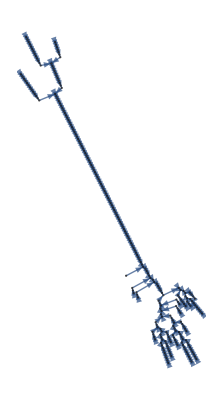

```mathematica
Graph[
DeleteDuplicates@Flatten[
Table[collatzGraph[{},i],{i,1,100}]
,1],
GraphLayout->"RadialEmbedding"]
```

```mathematica
Map[
Labeled[#,#]&,
DeleteDuplicates[
Flatten[
Table[
Map[
{First[#],Last[#]}&,
collatzGraph[{},i]],
{i, 1, 100}],
2]]]
```

{11,22,33,1010,55,1616,88,44,66,77,2222,1111,3434,1717,5252,2626,1313,4040,2020,99,2828,1414,1212,1515,4646,2323,7070,3535,106106,5353,160160,8080,1818,1919,5858,2929,8888,4444,2121,6464,3232,2424,2525,7676,3838,2727,8282,4141,124124,6262,3131,9494,4747,142142,7171,214214,107107,322322,161161,484484,242242,121121,364364,182182,9191,274274,137137,412412,206206,103103,310310,155155,466466,233233,700700,350350,175175,526526,263263,790790,395395,11861186,593593,17801780,890890,445445,13361336,668668,334334,167167,502502,251251,754754,377377,11321132,566566,283283,850850,425425,12761276,638638,319319,958958,479479,14381438,719719,21582158,10791079,32383238,16191619,48584858,24292429,72887288,36443644,18221822,911911,27342734,13671367,41024102,20512051,61546154,30773077,92329232,46164616,23082308,11541154,577577,17321732,866866,433433,13001300,650650,325325,976976,488488,244244,122122,6161,184184,9292,3030,3333,100100,5050,3636,3737,112112,5656,3939,118118,5959,178178,8989,268268,134134,6767,202202,101101,304304,152152,4242,4343,130130,6565,196196,9898,4949,148148,7474,4545,136136,6868,4848,5151,154154,7777,232232,116116,5454,5555,166166,8383,250250,125125,376376,188188,5757,172172,8686,6060,6363,190190,9595,286286,143143,430430,215215,646646,323323,970970,485485,14561456,728728,6666,6969,208208,104104,7272,7373,220220,110110,7575,226226,113113,340340,170170,8585,256256,128128,7878,7979,238238,119119,358358,179179,538538,269269,808808,404404,8181,8484,8787,262262,131131,394394,197197,592592,296296,9090,9393,280280,140140,9696,9797,292292,146146,9999,298298,149149,448448,224224}

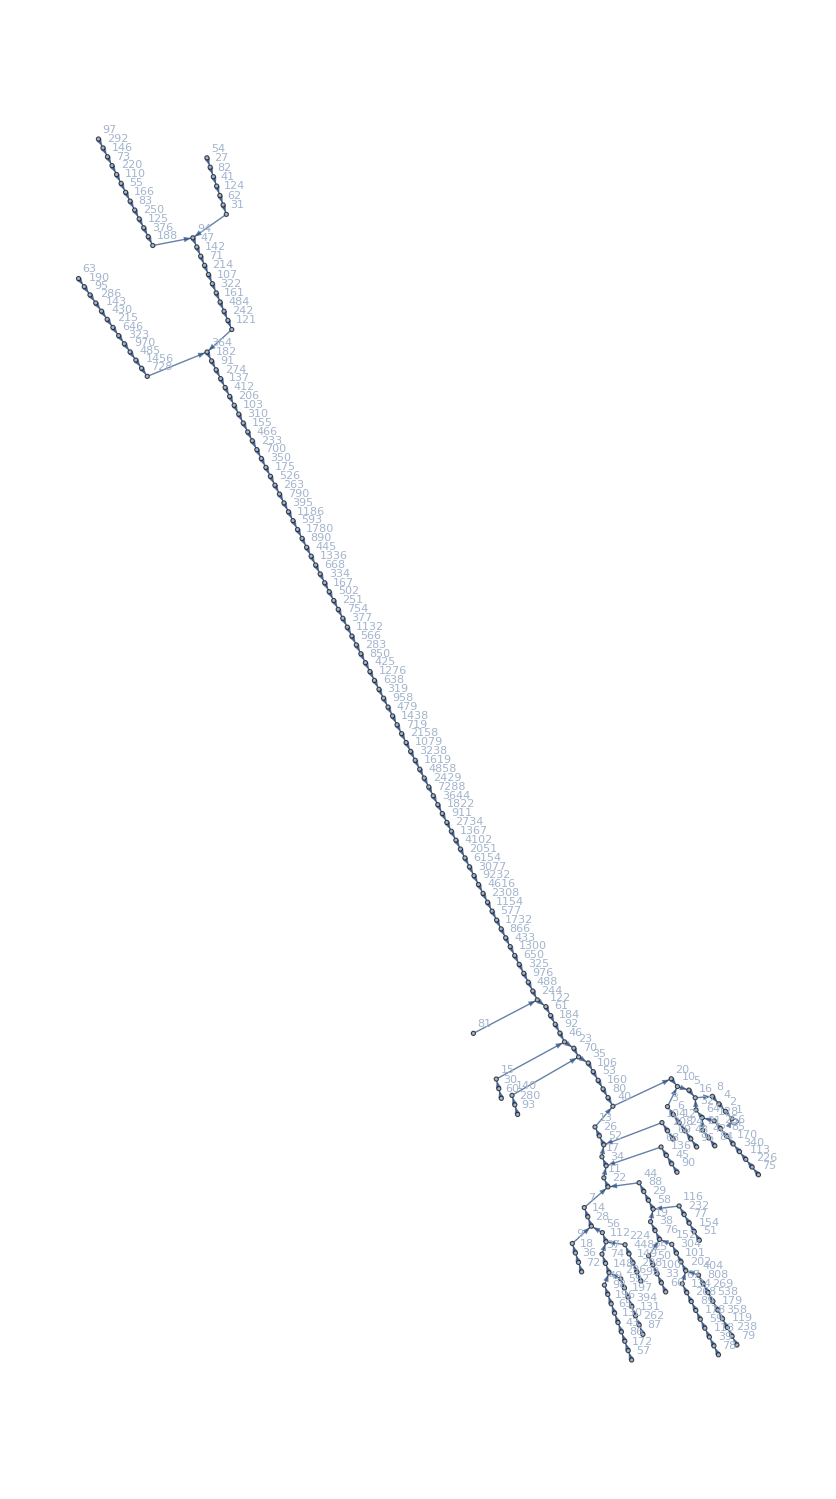

```mathematica
With[{limit=100},
Graph[
Map[
Labeled[#,#]&,
DeleteDuplicates[
Flatten[
Table[
Map[
{First[#],Last[#]}&,
collatzGraph[{},i]],
{i, 1, limit}],
2]]],
DeleteDuplicates@Flatten[
Table[collatzGraph[{},i],{i,1,limit}]
,1],
GraphLayout->"RadialEmbedding"]]
```

```mathematica
Manipulate[
Graph[
Map[
Labeled[#,#]&,
DeleteDuplicates[
Flatten[
Table[
Map[
{First[#],Last[#]}&,
collatzGraph[{},i]],
{i, 1, limit}],
2]]],
DeleteDuplicates@Flatten[
Table[collatzGraph[{},i],{i,1,limit}]
,1],
GraphLayout->"RadialEmbedding"],
{limit, 1, 100,1}]
```



```mathematica
CompleteGraph[3]
```

```mathematica
VertexCount[Graph[{1, 2, 3}, {Null, SparseArray[Automatic, {3, 3}, 0, {1, {{0, 2, 4, 6}, {{2}, {3}, {1}, {3}, {1}, {2}}}, Pattern}]}, {GraphLayout -> "CircularEmbedding"}]]
```

3

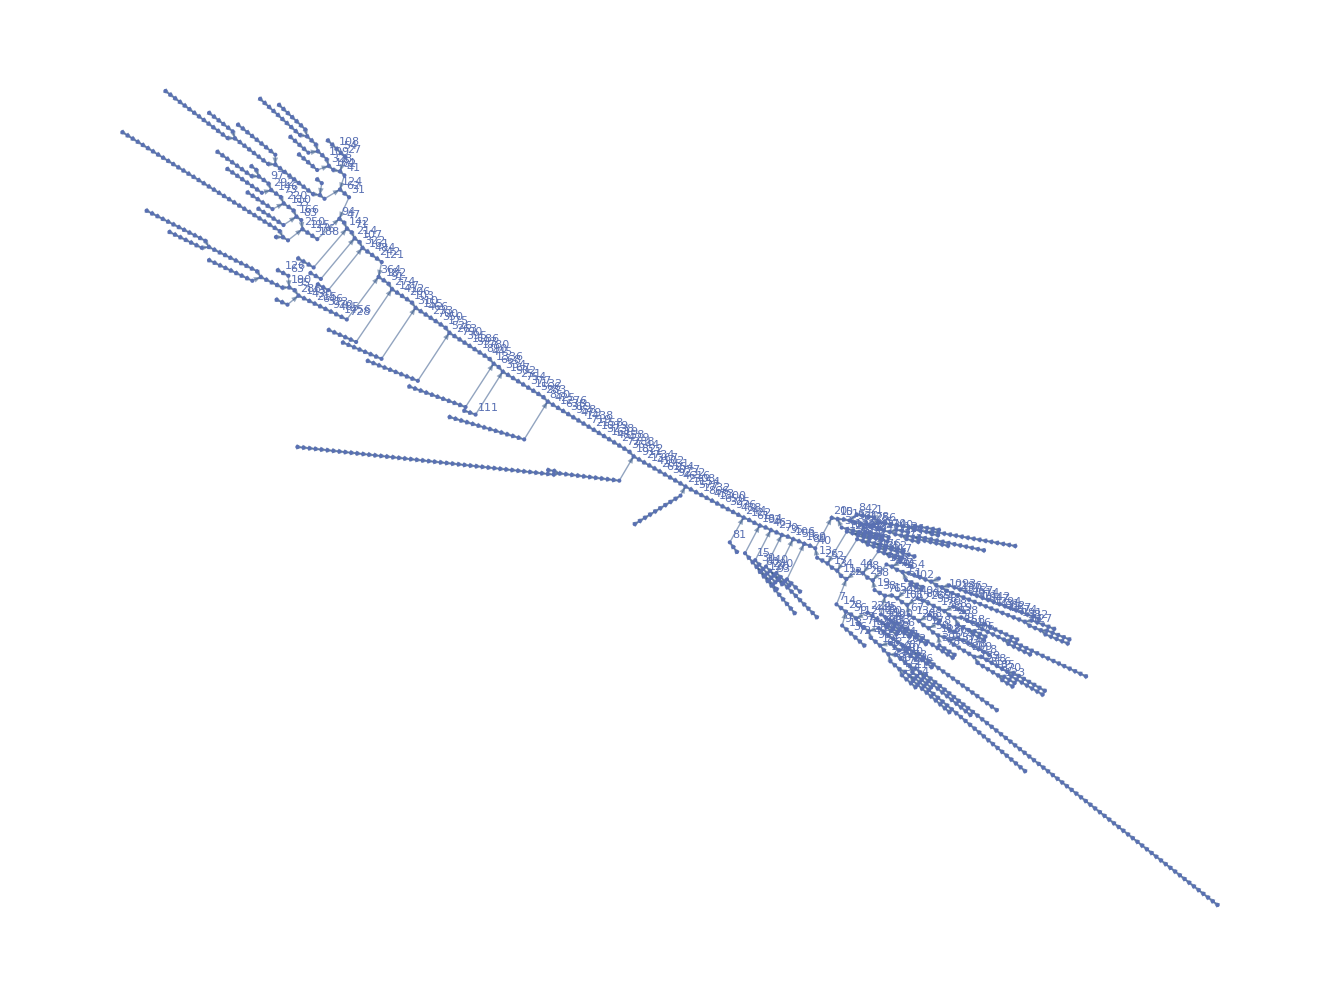

```mathematica
With[{limit=500},
Graph[
Map[
Labeled[#,#]&,
DeleteDuplicates[
Flatten[
Table[
Map[
{First[#],Last[#]}&,
collatzGraph[{},i]],
{i, 1, limit}],
2]]],
DeleteDuplicates@Flatten[
Table[collatzGraph[{},i],{i,1,limit}]
,1],
GraphLayout->"RadialEmbedding"]]
```

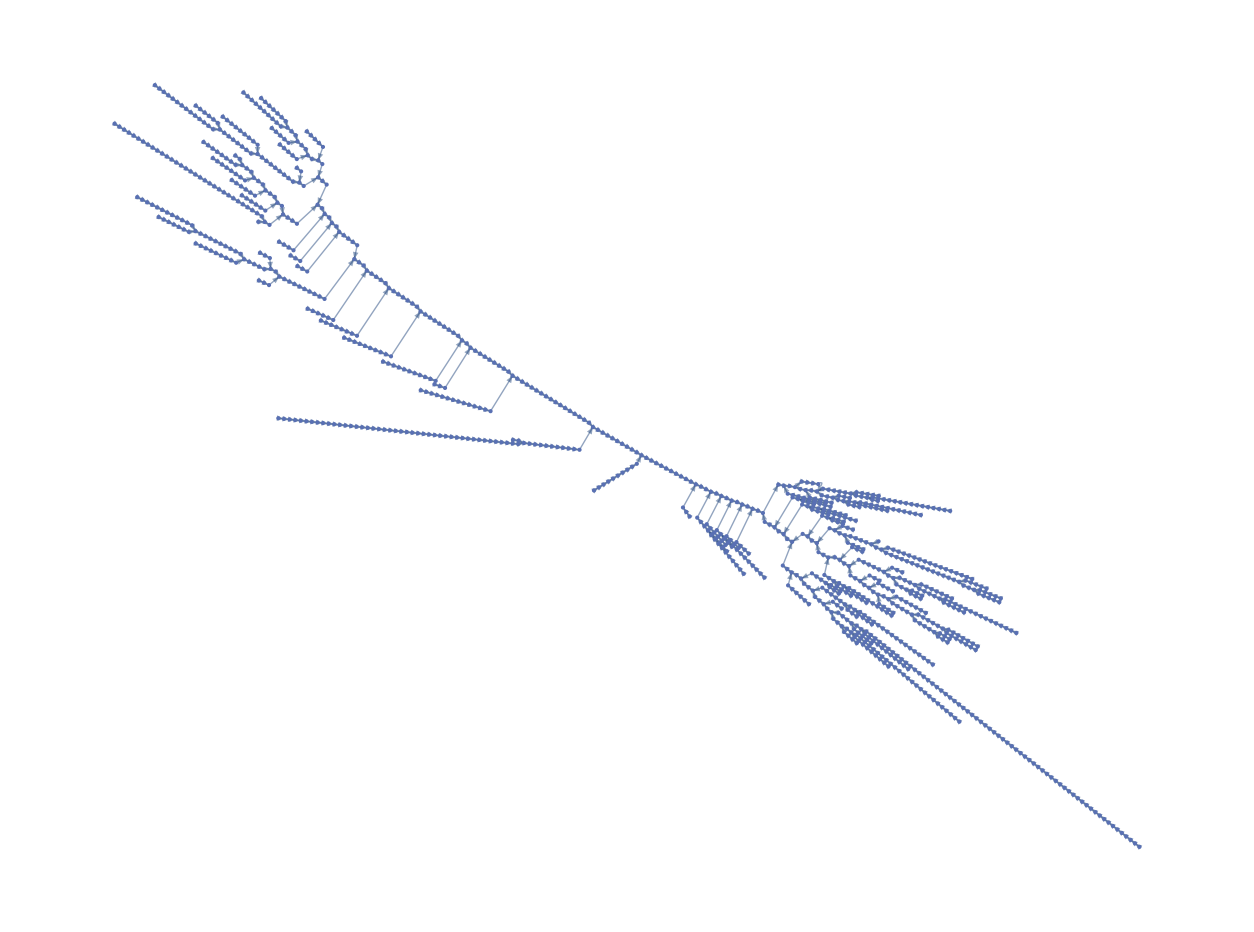

```mathematica
Graph[
DeleteDuplicates@Flatten[
Table[collatzGraph[{},i],{i,1,500}]
,1],
GraphLayout->"RadialEmbedding"]
```

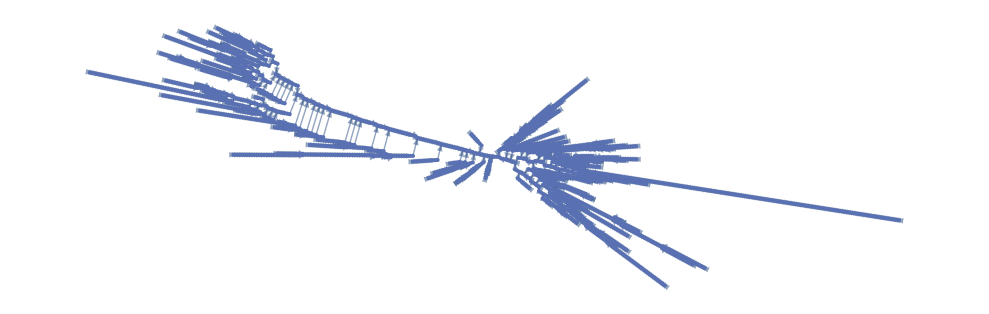

```mathematica
Graph[
DeleteDuplicates@Flatten[
Table[collatzGraph[{},i],{i,1,1000}]
,1],
GraphLayout->"RadialEmbedding"]
```

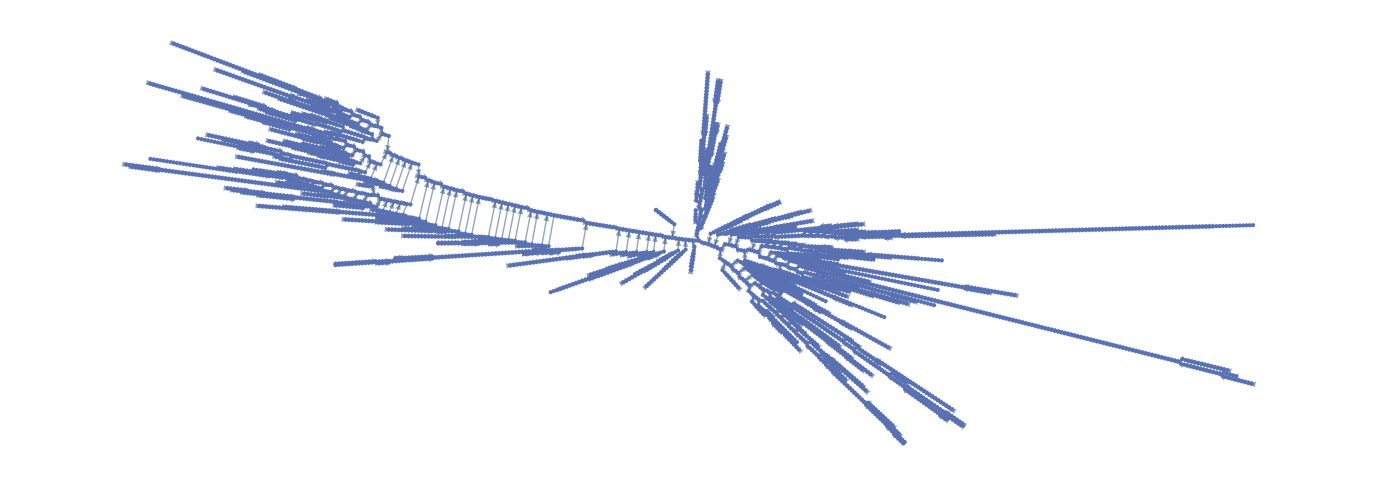

```mathematica
Graph[
DeleteDuplicates@Flatten[
Table[collatzGraph[{},i],{i,1,2000}]
,1],
GraphLayout->"RadialEmbedding"]
```

```mathematica
AcyclicGraphQ[%219]
```

True

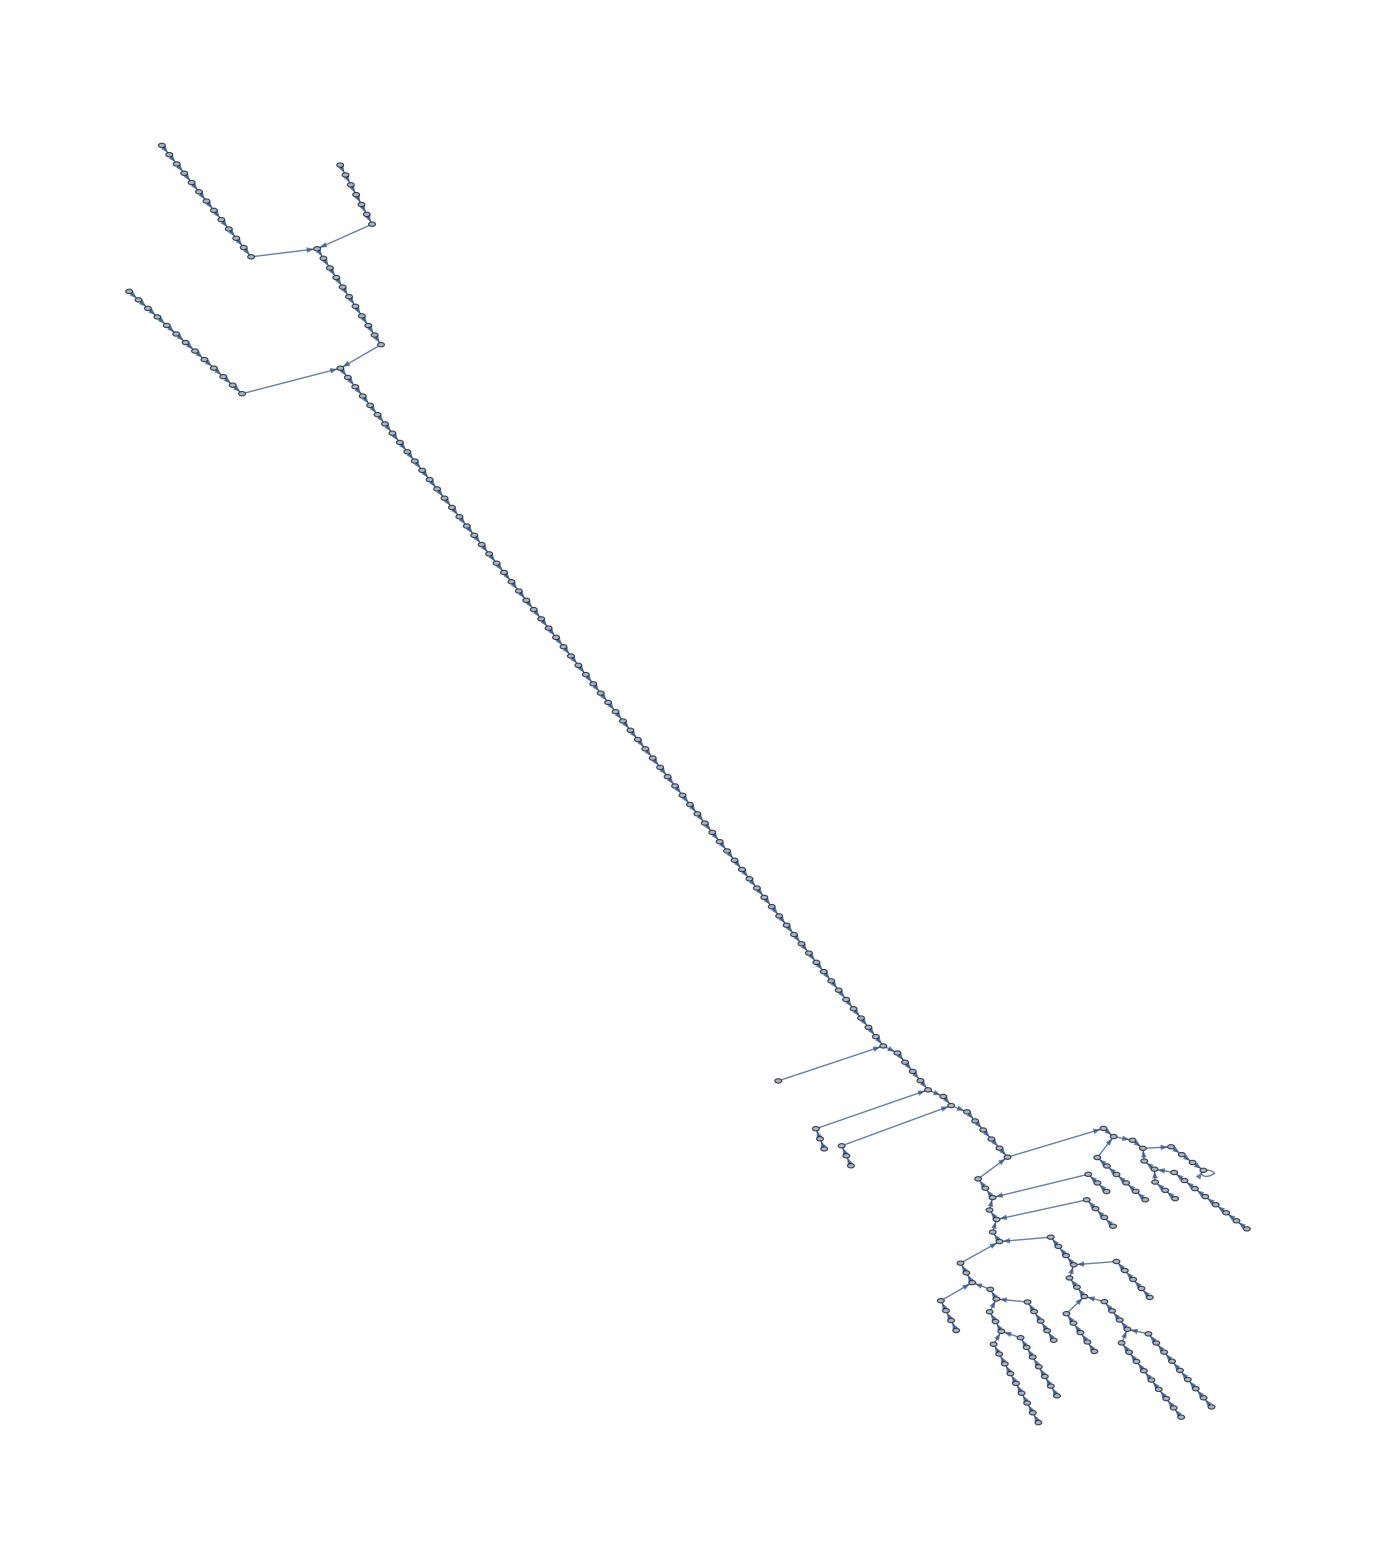

```mathematica
Graph[
DeleteDuplicates@Flatten[
Table[collatzGraph[{},i],{i,1,100}]
,1],
GraphLayout->"RadialEmbedding"]
```

```mathematica
FindShortestPath[%221,27,1]
```

{27,82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

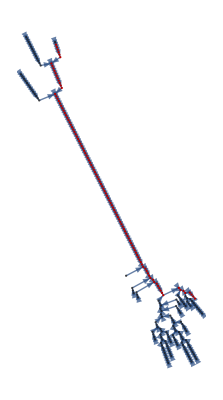

```mathematica
HighlightGraph[Graph[{1,2,3,10,5,16,8,4,6,7,22,11,34,17,52,26,13,40,20,9,28,14,12,15,46,23,70,35,106,53,160,80,18,19,58,29,88,44,21,64,32,24,25,76,38,27,82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,30,33,100,50,36,37,112,56,39,118,59,178,89,268,134,67,202,101,304,152,42,43,130,65,196,98,49,148,74,45,136,68,48,51,154,77,232,116,54,55,166,83,250,125,376,188,57,172,86,60,63,190,95,286,143,430,215,646,323,970,485,1456,728,66,69,208,104,72,73,220,110,75,226,113,340,170,85,256,128,78,79,238,119,358,179,538,269,808,404,81,84,87,262,131,394,197,592,296,90,93,280,140,96,97,292,146,99,298,149,448,224},{{{1,1},{2,1},{3,4},{4,5},{5,6},{6,7},{7,8},{8,2},{9,3},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,4},{20,21},{21,22},{22,10},{23,9},{24,25},{25,26},{26,27},{27,28},{28,29},{29,30},{30,31},{31,32},{32,18},{33,20},{34,35},{35,36},{36,37},{37,38},{38,11},{39,40},{40,41},{41,6},{42,23},{43,44},{44,45},{45,34},{46,47},{47,48},{48,49},{49,50},{50,51},{51,52},{52,53},{53,54},{54,55},{55,56},{56,57},{57,58},{58,59},{59,60},{60,61},{61,62},{62,63},{63,64},{64,65},{65,66},{66,67},{67,68},{68,69},{69,70},{70,71},{71,72},{72,73},{73,74},{74,75},{75,76},{76,77},{77,78},{78,79},{79,80},{80,81},{81,82},{82,83},{83,84},{84,85},{85,86},{86,87},{87,88},{88,89},{89,90},{90,91},{91,92},{92,93},{93,94},{94,95},{95,96},{96,97},{97,98},{98,99},{99,100},{100,101},{101,102},{102,103},{103,104},{104,105},{105,106},{106,107},{107,108},{108,109},{109,110},{110,111},{111,112},{112,113},{113,114},{114,115},{115,116},{116,117},{117,118},{118,119},{119,120},{120,121},{121,122},{122,123},{123,124},{124,125},{125,126},{126,127},{127,128},{128,129},{129,130},{130,131},{131,132},{132,133},{133,134},{134,135},{135,136},{136,137},{137,138},{138,139},{139,140},{140,25},{141,24},{142,143},{143,144},{144,43},{145,33},{146,147},{147,148},{148,21},{149,150},{150,151},{151,152},{152,153},{153,154},{154,155},{155,156},{156,157},{157,158},{158,159},{159,160},{160,44},{161,39},{162,163},{163,164},{164,165},{165,166},{166,167},{167,168},{168,169},{169,146},{170,171},{171,172},{172,13},{173,42},{174,175},{175,176},{176,177},{177,178},{178,35},{179,46},{180,181},{181,182},{182,183},{183,184},{184,185},{185,186},{186,52},{187,188},{188,189},{189,162},{190,141},{191,192},{192,193},{193,194},{194,195},{195,196},{196,197},{197,198},{198,199},{199,200},{200,201},{201,202},{202,203},{203,63},{204,142},{205,206},{206,207},{207,15},{208,145},{209,210},{210,211},{211,180},{212,213},{213,214},{214,215},{215,216},{216,217},{217,218},{218,219},{219,40},{220,149},{221,222},{222,223},{223,224},{224,225},{225,226},{226,227},{227,228},{228,229},{229,157},{230,136},{231,161},{232,233},{233,234},{234,235},{235,236},{236,237},{237,238},{238,168},{239,170},{240,241},{241,242},{242,27},{243,173},{244,245},{245,246},{246,209},{247,248},{248,249},{249,250},{250,251},{251,147}},Null},{GraphLayout->"RadialEmbedding"}],PathGraph[%225]]
```

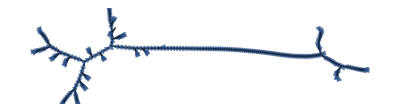

```mathematica
SimpleGraph[%221]
```

```mathematica
TopologicalSort[%221]
```

TopologicalSort[-Graphics-]

```mathematica
GraphCenter[%221]
```

{}